# 2D FEA Build

We want to solve the TWO dimensional damped wave equation
	u_tt+c u_t=k Δu
on a domain Ω with Dirichlet conditions u=0 on the boundary ∂Ω

Our spatial Weak Form is for all v∈H_0^1(Ω)

∫_Ω u_tt v dA +c∫_Ω u_t v dA =-k∫_Ω ∇u.∇v dA

We mesh the region with a VERY coarse mesh

We let the mesher pick the order for the vertices and triangles.

We do not need to solve for border vertices since the boundary conditions tell us u|_(∂Ω)=0.

We are going to use our FEA structure and manually build up the matrices for our FEA stuff.

The counting scheme for vertices and elements is no longer obvious.

The mesh is everything: the nodes; the triangles; the numbering scheme; and the connectivity information.

As before could people remind me to take pics of the board as we go.

## Mesh Pic

Simple labelled mesh

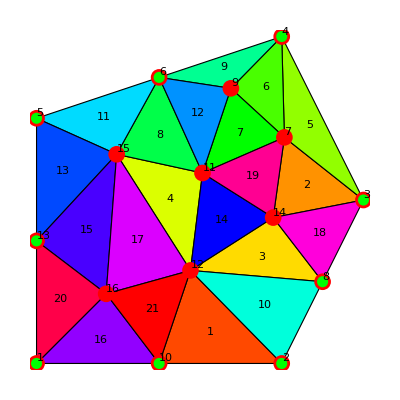

```mathematica
TestMesh=DiscretizeRegion[Polygon[{{0,0},{3,0},{4,2},{3,4},{0,3}}],
MaxCellMeasure->0.9];
TestTriangles = MeshCells[TestMesh,2]; m=Length[TestTriangles];
{AllPoints,BoundaryPoints}=Map[ MeshCoordinates,{TestMesh,BoundaryMesh[TestMesh]}];
Graphics[{ EdgeForm[Black],
Table[
{j1,j2,j3}=TestTriangles⟦i,1⟧;
{p1,p2,p3}=AllPoints⟦{j1,j2,j3}⟧;
{{Hue[i/m],Polygon[{p1,p2,p3}]}, Text[i,(p1+p2+p3)/3]},
{i,1,m}],
{Red, PointSize[0.03],Point[AllPoints]},
{Green,PointSize[0.02],Point[BoundaryPoints]},
Table[p=AllPoints⟦j⟧;
Text[j,p,{-1,-1},Background->White],
{j,1,Length[AllPoints]}]
}]
```

## Reference and Physical Slab Functions

The reference triangle has simple “slab” function formulas.  We transform theses simple slab function to physical slab functions with the reference map (X
Y)->J.(X
Y)+(p⃗)_1 where J=[(p⃗)_2-(p⃗)_1|(p⃗)_3-(p⃗)_1] i.e. the vectors are columns of the matrix J.  The inverse map is also simple (x
y)->J^-1.((x
y)-(p⃗)_1).

```mathematica
RefSlab[i_][{X_,Y_}]:=Switch[i,
1,{X,Y,1-X-Y},
2,{X,Y,X},
3, {X,Y,Y}]
Slab[i_,{p1_,J_}][{X_,Y_}]:=Module[{x,y},
{x,y}=p1+J.{X,Y};
Switch[i,
1,{x,y,1-X-Y},
2,{x,y,X},
3, {x,y,Y}]]
slab[i_,{p1_,J_}][{x_,y_}]:=Module[{X,Y},
{X,Y}=Inverse[J].({x,y}-p1); 
Switch[i,
1,1-X-Y,
2,X,
3, Y]]
```

Here is a simple test!

```mathematica
{p1,p2,p3}={{1,1}, {3,1},{2,1+√3}};
J={p2-p1,p3-p1}ᵀ; InvJ=Inverse[J];
TabView[{
"Reference"->ParametricPlot3D[ {RefSlab[1][{X,Y}],RefSlab[2][{X,Y}],RefSlab[3][{X,Y}]},{X,0,1},{Y,0,1-X},
Mesh->True], 
"Physical"->ParametricPlot3D[ {Slab[1,{p1,J}][{X,Y}],Slab[2,{p1,J}][{X,Y}],Slab[3,{p1,J}][{X,Y}]},{X,0,1},{Y,0,1-X},
Mesh->True,
BoxRatios->{1,1,1}],
"physical"->Plot3D[ {slab[1,{p1,J}][{x,y}],slab[2,{p1,J}][{x,y}],slab[3,{p1,J}][{x,y}]},
{x,y}∈Polygon[{p1,p2,p3}],
Mesh->True,
BoxRatios->{1,1,1}]
}]
```

```mathematica
123
```

The best thing about this way of thinking is that it works for all sorts of other elements and shape functions.

## Chain Rule: General

We need gradients with respect to the physical coordinates {x,y}.  We have simple formulas for the reference slab (and other fancier) functions. 
We need to remember the chain rule from Calc III
	D_{x,y}(F[G[{x,y}]])=DF[G[{x,y}]] DG[{x,y}]
I know it has way too many brackets and stuff.  We should check!

### Test (Analytical)

Lets make up an example!

```mathematica
Clear[x,y,X,Y]
G[{x_,y_}]:={Sin[x y]+ x^2+y,Cos[x+y^2]+2 x + 1}
F[{X_,Y_}]:= X^2+ Y + ArcTan[X+Y Sin[X+Y]]
DG[{x_,y_}]=D[G[{x,y}],{{x,y}}]
DF[{X_,Y_}]=D[F[{X,Y}],{{X,Y}}]
```

{{2 x+y Cos[x y],1+x Cos[x y]},{2-Sin[x+y^2],-2 y Sin[x+y^2]}}

{2 X+(1+Y Cos[X+Y])/(1+(X+Y Sin[X+Y])^2),1+(Y Cos[X+Y]+Sin[X+Y])/(1+(X+Y Sin[X+Y])^2)}

```mathematica
Simplify[D[ F[G[{x,y}]],{{x,y}}]-DF[G[{x,y}]].DG[{x,y}]]
```

{0,0}

### Test (Numerical)

We should test this

```mathematica
{x,y}={1.2,3.4};
{X,Y}=G[{x,y}];
u=Normalize[RandomReal[{-1,1},2]];
h = 0.001;
(F[G[{x,y}+ h u] ]- F[G[{x,y}]])/h
(F[G[{x,y}+ h u] ]- F[G[{x,y}- h u]])/(2h)
DF[{X,Y}].DG[{x,y}].u
```

-4.87762

-4.91832

-4.91826

## Chain Rule: FEA

The connection between {x,y} and {X,Y} is linear in our case so we have that the relation ship between the {x,y} gradient and the easy {X,Y} computation is much simpler.

## Building Matrices

Here is our mesh again.  Remember we are going through the triangles in order and adding the pieces of the stiffness and mass matrices in the correct entries as we go.

```mathematica
TestMesh=DiscretizeRegion[Polygon[{{0,0},{3,0},{4,2},{3,4},{0,3}}],
MaxCellMeasure->0.9];
TestTriangles = MeshCells[TestMesh,2]; m=Length[TestTriangles];
{AllPoints,BoundaryPoints}=Map[ MeshCoordinates,{TestMesh,BoundaryMesh[TestMesh]}];
Graphics[{ EdgeForm[Black],
Table[
{j1,j2,j3}=TestTriangles⟦i,1⟧;
{p1,p2,p3}=AllPoints⟦{j1,j2,j3}⟧;
{{Hue[i/m],Polygon[{p1,p2,p3}]}, Text[i,(p1+p2+p3)/3]},
{i,1,m}],
{Red, PointSize[0.03],Point[AllPoints]},
{Green,PointSize[0.02],Point[BoundaryPoints]},
Table[p=AllPoints⟦j⟧;
Text[j,p,{-1,-1},Background->White],
{j,1,Length[AllPoints]}]
}]
```

-Graphics-

We need to know how to build an “empty” sparse matrix “A” of the appropriate size.  We are going to do all the vertices as a start.  Then we need to know how to add entries to “A”.

```mathematica
{m,n}=Map[Length,{AllPoints,TestTriangles}]
A=SparseArray[{},{m,m}]
```

{16,21}

SparseArray[…]